```mathematica
D2approx[n_,j_]:=(-1)^j (1-(Gamma[j,-Log[n]])/Gamma[j])
D2sapprox[n_,k_,s_]:=(-1)^k((Gamma[k,0,-(1-s) Log[n]]) (1-s)^-k)/Gamma[k]
Dl2sapprox[n_,j_,s_]:=If[j==0,Limit[(-1)^k((Gamma[k,0,-(1-s) Log[n]]) (1-s)^-k)/Gamma[k],{k->j}],(-1)^j((Gamma[j,0,-(1-s) Log[n]]) (1-s)^-j)/Gamma[j]]
Dapprox[n_,z_]:=Sum[FactorialPower[z,a]/a! D2approx[n,a],{a,0,2000}]
Dsapprox[n_,z_,s_]:=Sum[FactorialPower[z,a]/a! D2sapprox[n,a,s],{a,1,2000}]
EtaApprox[n_, z_]:=(1-2^(1-z))Dapprox[n,z]
EtaApprox2[n_, k_, b_, s_]:=Sum[(-1)^j Binomial[k,j] b^(j(1-s))  Dsapprox[n/b^j,k,s],{j,0,k}]
```

```mathematica
N[EtaApprox[100,-1]]
```

10.8155-5.11208×10^-13 ⅈ

```mathematica
EtaApprox2[100,1,2,ZetaZero[1]]
```

(2^(1-ZetaZero[1]) (1-50^(1-ZetaZero[1])))/(1-ZetaZero[1])-(1-100^(1-ZetaZero[1]))/(1-ZetaZero[1])

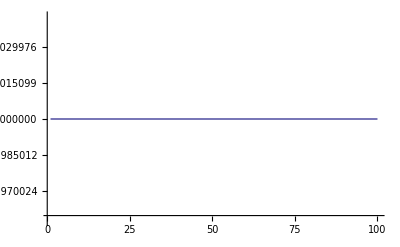

```mathematica
Plot[EtaApprox2[n,1,2,0],{n,1,100}]
```

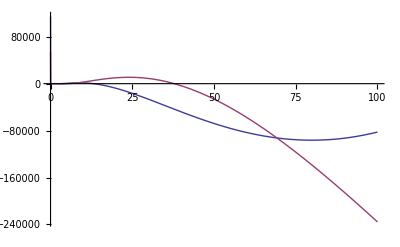

```mathematica
Plot[{Re[EtaApprox[n,ZetaZero[1]]],Im[EtaApprox[n,ZetaZero[1]]]},{n,0,100}]
```

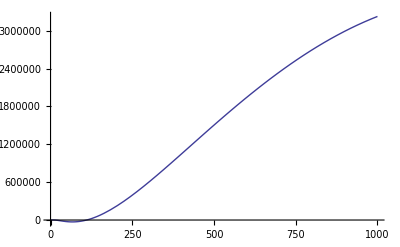

```mathematica
Plot[{Re[Dapprox[n,1-ZetaZero[1]]]},{n,0,1000}]
```

```mathematica
Plot[{Re[Dapprox[n,ZetaZero[1]]]},{n,0,1000}]
```

-Graphics-

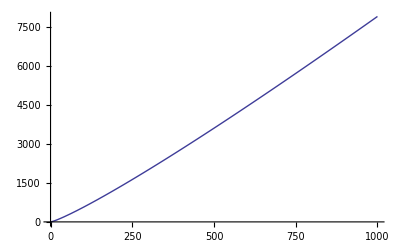

```mathematica
Plot[{Re[Dapprox[n,2]]},{n,0,1000}]
```

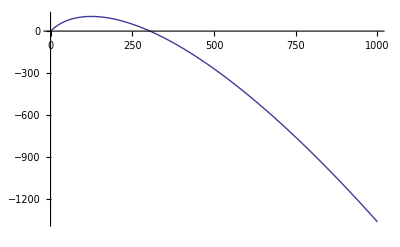

```mathematica
Plot[{Re[Dapprox[n,2+I]]},{n,0,1000}]
```

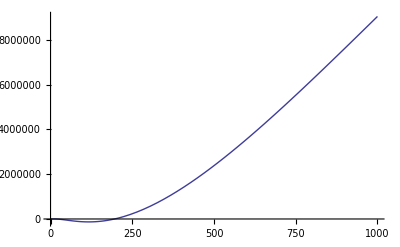

```mathematica
Plot[{Re[Dapprox[n,2+14I]]},{n,0,1000}]
```

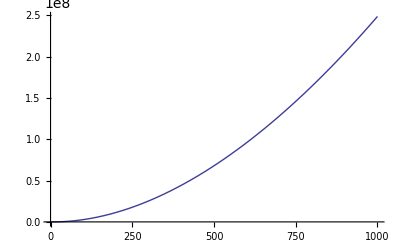

```mathematica
Plot[{Re[Dapprox[n,12]]},{n,0,1000}]
```

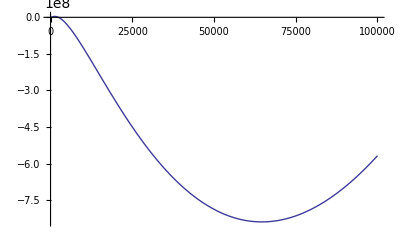

```mathematica
Plot[{Re[Dapprox[n,ZetaZero[1]]]},{n,0,100000}]
```

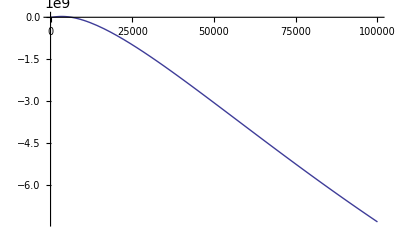

```mathematica
Plot[{Re[Dapprox[n,2+14I]]},{n,0,100000}]
```

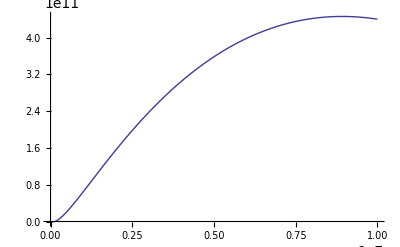

```mathematica
Plot[{Re[Dapprox[n,ZetaZero[1]]]},{n,0,10000000}]
```

```mathematica
Plot[{Re[Dapprox[n,1/2 + 13 I]]},{n,0,10000000}]
```

$Aborted

```mathematica
t[s_]:=N[Sum[(-1)^(j+1)/j^s,{j,1,1000000}]]
```

```mathematica
t[ZetaZero[2]]
```

-0.0000831614+0.000493036 ⅈ

```mathematica
Sum[(-1)^(j+1)/j^ZetaZero[2],{j,1,Infinity}]
```

0

```mathematica
N[Pi^2/12]
```

0.822467